```mathematica
ClearAll["Global`*"]
(*別のnbファイルの内容を取り込み，後で利用する*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]];
```

```mathematica
periods=Table[i,{i,30,70,5}];
names=Table["dataMP1d5_T0d"<>ToString@periods[[i]],{i,1,Length[periods]}];

periods=Table[i,{i,30,70,5}]
names=Table["dataMP3d0_T0d"<>ToString@periods[[i]],{i,1,Length[periods]}]

periods=Table[i,{i,30,70,5}]
names=Table["dataMP5d0_T0d"<>ToString@periods[[i]],{i,1,Length[periods]}]
```

{30,35,40,45,50,55,60,65,70}

{dataMP3d0_T0d30,dataMP3d0_T0d35,dataMP3d0_T0d40,dataMP3d0_T0d45,dataMP3d0_T0d50,dataMP3d0_T0d55,dataMP3d0_T0d60,dataMP3d0_T0d65,dataMP3d0_T0d70}

{30,35,40,45,50,55,60,65,70}

{dataMP5d0_T0d30,dataMP5d0_T0d35,dataMP5d0_T0d40,dataMP5d0_T0d45,dataMP5d0_T0d50,dataMP5d0_T0d55,dataMP5d0_T0d60,dataMP5d0_T0d65,dataMP5d0_T0d70}

```mathematica
files=Table["実験結果20250116/"<>names[[i]]<>".csv",{i,1,Length@names}]
DATA=Table[Import[FileNameJoin[{NotebookDirectory[],files[[i]]}],"CSV"],{i,1,Length[files],1}];
colorFunc=Blend[{Cyan,Blue,Red},#/Length[DATA]]&;
colorPitch=Blend[{Cyan,Blue,Red},#/Length[DATA]]&;
colorHeave=Blend[{Yellow,Red,Black},#/Length[DATA]]&;
```

{実験結果20250116/dataMP5d0_T0d30.csv,実験結果20250116/dataMP5d0_T0d35.csv,実験結果20250116/dataMP5d0_T0d40.csv,実験結果20250116/dataMP5d0_T0d45.csv,実験結果20250116/dataMP5d0_T0d50.csv,実験結果20250116/dataMP5d0_T0d55.csv,実験結果20250116/dataMP5d0_T0d60.csv,実験結果20250116/dataMP5d0_T0d65.csv,実験結果20250116/dataMP5d0_T0d70.csv}

```mathematica
(*関数定義*)
calculate[data_]:=Module[{min,max,m,xaxis,yaxis,ans,zaxis,CameraM,anlgetable,timetable,a00,a01,a02,a10,a11,a12,a20,a21,a22,displacement,initCOM,COM},
min=100;
max=380;
max=If[max>Length[data],Length[data],max];
ydir[i_]:=Normalize[data[[i]][[8;;10]]-data[[i]][[2;;4]]];
zdir[i_]:=Normalize[Cross[data[[i]][[5;;7]]-data[[i]][[2;;4]],data[[i]][[8;;10]]-data[[i]][[2;;4]]]];
xdir[i_]:=Normalize[Cross[ydir[i],zdir[i]]];
xaxis=Mean[Table[xdir[i],{i,5,50}]];
yaxis=Mean[Table[ydir[i],{i,5,50}]];
zaxis=Mean[Table[zdir[i],{i,5,50}]];
(*カメラの座標系から水槽x,y,z座標へ変換するための，回転行列を計算する*)
m={{a00,a01,a02},{a10,a11,a12},{a20,a21,a22}};
ans=Quiet@FindMinimum[Norm[m.xaxis-{1,0,0}]+Norm[m.yaxis-{0,1,0}]+Norm[m.zaxis-{0,0,1}],{a00,a01,a02,a10,a11,a12,a20,a21,a22}];
CameraM=m/.ans[[2]];
(*table=Table[{data[[i,1]],VectorAngle[M.zdir[i],{0,0,1}]},{i,1,100}];*)
(*displacement=Table[M.(data[[i]][[2;;4]]-data[[1]][[2;;4]]+data[[i]][[5;;7]]-data[[1]][[5;;7]]+data[[i]][[8;;10]]-data[[1]][[8;;10]]),{i,min,max}];*)
COM[i_]:=(data[[i]][[2;;4]]+data[[i]][[5;;7]]+data[[i]][[8;;10]])/3;
initCOM=Mean[Table[COM[i],{i,10,min}]];
displacement=Table[CameraM.(COM[i]-initCOM),{i,min,max}];

anlgetable=Table[VectorAngle[CameraM.zdir[i],{0,0,1}],{i,min,max}];
timetable=Table[data[[i,1]],{i,min,max}];
{displacement,anlgetable,timetable,CameraM,{xaxis,yaxis,zaxis},{min,max}}
]
```

```mathematica
inv[x_]:=If[Abs[x]>10^-10,1/x,1/10^-10];
```

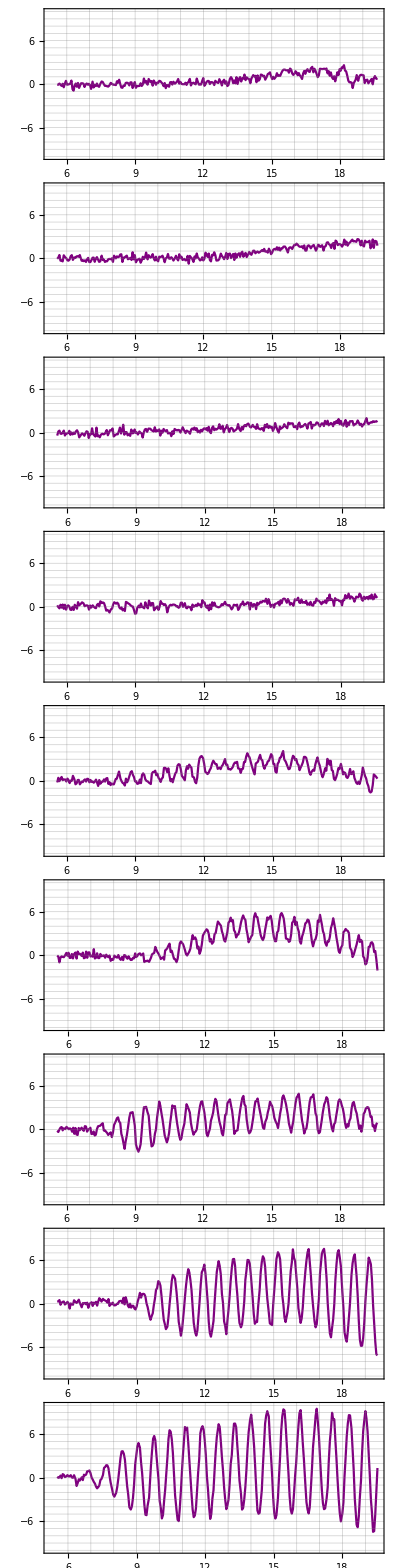

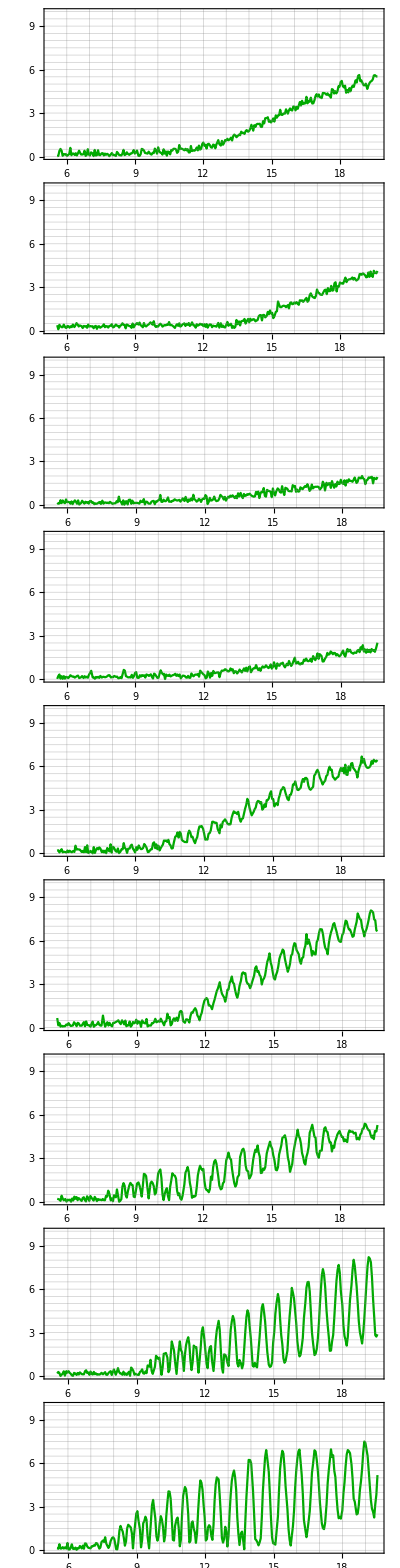

```mathematica
Column@Table[
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
ListPlot[Transpose[{timetable,displacement[[;;,3]]}],ImageSize->800,AspectRatio->1/10,PlotRange->{Automatic,{-10,10}},GridLines->All,PlotLegends->Automatic,Evaluate[plot2Doption],(*FrameLabel->{"Time [s]","Heave [mm]"},*)PlotStyle->Purple]
,{i,1,Length[DATA]}]

Column@Table[
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
ListPlot[Transpose[{timetable,anlgetable/π*180}],ImageSize->800,AspectRatio->1/10,PlotRange->{Automatic,{0,10}},Evaluate[plot2Doption],GridLines->All(*,FrameLabel->{"Time [s]","Pitch Angle [rad]"}*),ImageSize->Large,PlotStyle->Darker[Green]]
,{i,1,Length[DATA]}]
```

## ピッチ

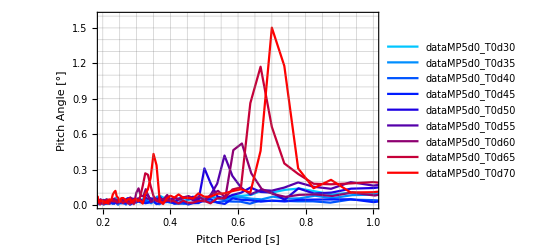

```mathematica
(*フーリエ解析*)
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2/π*180}&@@@interpolateAndFourier[timetable,anlgetable]]]
,{i,1,Length@DATA,1}]
,PlotLegends->names
,GridLines->All
,PlotRange->{{0.2,1},{0,1.6}}
,Evaluate[plot2Doption]
,FrameLabel->{"Pitch Period [s]","Pitch Angle [°]"}
,PlotStyle->Table[colorFunc[i],{i,1,Length[DATA]}]
]
```

```mathematica
option3D={Filling->Axis
,ViewPoint->{-Pi,-Pi,Pi/2}
,PlotStyle->Black
(*,PlotLegends->Placed[names, Top]*)
,LabelStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->18]
,PlotRange->Automatic
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->18]
,ImageSize->600
,AxesStyle->Black
,Axes->True};
```

```mathematica
ListLinePlot3D[
Table[
Module[{tmp},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
tmp=interpolateAndFourier[timetable,anlgetable];
Table[{0.01*periods[[i]],inv@tmp[[j]][[1]],tmp[[j]][[2]]/π*180},{j,1,Length@tmp}]
]
,{i,1,Length@DATA,1}]
,ImageSize->Large
,ViewPoint->{-Pi,Pi,2}
,PlotRange->{All,{0.2,1},{0,1.6}}
,ScalingFunctions->{Identity,"Reverse",Identity}  (*y軸だけを反転*)
,AxesLabel->{"Incident Wave Period [s]","Pitch Period [s]",Rotate["Pitch Angle [°]",π/2]}
,PlotStyle->Table[colorFunc[i],{i,1,Length[DATA]}]
,Evaluate[option3D]
]
```

-Graphics3D-

## ヒーブ

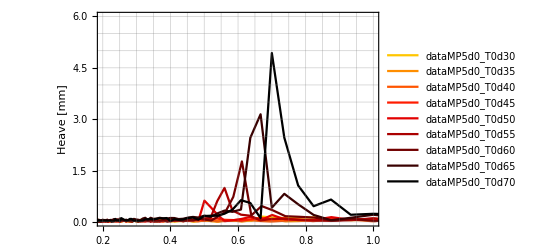

```mathematica
(*フーリエ解析*)
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2}&@@@interpolateAndFourier[timetable,displacement[[;;,3]]]]]
,{i,1,Length@DATA,1}]
,PlotLegends->names
,GridLines->All
,PlotRange->{{0.2,1},{0,6}}
,Evaluate[plot2Doption]
,PlotStyle->Table[colorHeave[i],{i,1,Length[DATA]}]
,FrameLabel->{""(*"Heave Period [s]"*),"Heave [mm]"}
]
```

```mathematica
ListLinePlot3D[
Table[
Module[{tmp},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
tmp=interpolateAndFourier[timetable,displacement[[;;,3]]];
Table[{0.01*periods[[i]],inv@tmp[[j]][[1]],tmp[[j]][[2]]},{j,1,Length@tmp}]
]
,{i,1,Length@DATA,1}]
,ImageSize->Large
,ViewPoint->{-Pi,Pi,2}
,PlotRange->{All,{0.2,1},{0,6}}  (*y軸を反転させる*)
 ,ScalingFunctions->{Identity,"Reverse"}  (*y軸だけを反転*)
,PlotStyle->Table[colorHeave[i],{i,1,Length[DATA]}]
,AxesLabel->{""(*"Incident Wave Period [s]"*),""(*"Heave Period [s]"*),Rotate["Heave [mm]",π/2]}
,Evaluate[option3D]
]
```

-Graphics3D-

```mathematica
data=DATA[[1]];
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[data];
center[i_]:=(data[[i]][[2;;4]]+data[[i]][[5;;7]]+data[[i]][[8;;10]])/3;
center0=center[1];
trfm[xyz_]:=M.(xyz-center0);
o={0,0,0};

Show[
{ListPointPlot3D[
{Table[trfm@data[[i]][[2;;4]],{i,min,max}],
Table[trfm@data[[i]][[5;;7]],{i,min,max}],
Table[trfm@data[[i]][[8;;10]],{i,min,max}]}
,BoxRatios->{1, 1, 1}
,AxesLabel->{"x","y","z"}
,PlotRange->{{-300,300},{-300,300},{-300,300}}
],
Graphics3D[Table[Line[{trfm@data[[i]][[2;;4]],trfm@data[[i]][[5;;7]],trfm@data[[i]][[8;;10]],trfm@data[[i]][[2;;4]]}],{i,min,max}]],
Graphics3D[{Red,Arrow[{o,o+200*xaxis}]}],
Graphics3D[{Blue,Arrow[{o,o+200*yaxis}]}],
Graphics3D[{Green,Arrow[{o,o+200*zaxis}]}]
}
,BoxRatios->{1, 1, 1}
,AxesLabel->{"x","y","z"}
,FrameTicks->True
,PlotRange->{{-300,300},{-300,300},{-300,300}}
];

Manipulate[
Show[
ListPointPlot3D[
{{trfm@data[[i]][[2;;4]]},
{trfm@data[[i]][[5;;7]]},
{trfm@data[[i]][[8;;10]]}}
,PlotLabel->data[[i]][[1]]
,PlotStyle->{Red,Blue,Green}
,PlotLabel->data[[i]][[1]]
,PlotRange->{{-300,300},{-300,300},{-300,300}}
,BoxRatios->{ 1, 1,1}
,AxesLabel->{"x","y","z"}
],
Graphics3D[{Thick,Line[{trfm@data[[i]][[2;;4]],trfm@data[[i]][[5;;7]],trfm@data[[i]][[8;;10]],trfm@data[[i]][[2;;4]]}]}],
Graphics3D[{Red,Arrow[{o,o+300*M.xaxis}]}],
Graphics3D[{Blue,Arrow[{o,o+300*M.yaxis}]}],
Graphics3D[{Green,Arrow[{o,o+300*M.zaxis}]}],
Graphics3D[{Purple,Thick,Arrow[{trfm@center[i],trfm@center[i]+300*M.zdir[i]}]}]
]
,{i,min,max,1}]

Show@Table[
Show[
ListPointPlot3D[
{{trfm@data[[i]][[2;;4]]},
{trfm@data[[i]][[5;;7]]},
{trfm@data[[i]][[8;;10]]}}
,PlotLabel->data[[i]][[1]]
,PlotStyle->{Red,Blue,Green}
,PlotLabel->data[[i]][[1]]
,PlotRange->{{-300,300},{-300,300},{-300,300}}
,BoxRatios->{ 1, 1,1}
,AxesLabel->{"x","y","z"}
],
Graphics3D[{Thick,Line[{trfm@data[[i]][[2;;4]],trfm@data[[i]][[5;;7]],trfm@data[[i]][[8;;10]],trfm@data[[i]][[2;;4]]}]}],
Graphics3D[{Red,Arrow[{o,o+300*M.xaxis}]}],
Graphics3D[{Blue,Arrow[{o,o+300*M.yaxis}]}],
Graphics3D[{Green,Arrow[{o,o+300*M.zaxis}]}],
Graphics3D[{Purple,Thick,Arrow[{trfm@center[i],trfm@center[i]+300*M.zdir[i]}]}]
]
,{i,min,max,10}]
```

-Graphics3D-